## SolutionVariables-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xlr8r.m;
<<Cellzilla2D.m
```

xCellerator 0.95 (28-Feb-2014) loaded Thu 15 Jun 2017 11:29:15
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Cellzilla2D (3.0.51f (14 June 2017)) loaded Thu 15 Jun 2017 11:29:15
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

Define a cellular template to run the model on.

4 cells

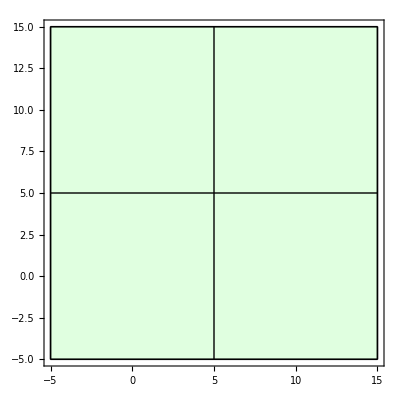

```mathematica
w=TemplateRectangularCover[10, 10, 10, 10, 0]; 
Print[n=NTissueCells[w]," cells"];
ShowTissue[w,Frame->True,"BoundaryStyle"->Black,"CellNumbers"->False]
```

## Test a simple network

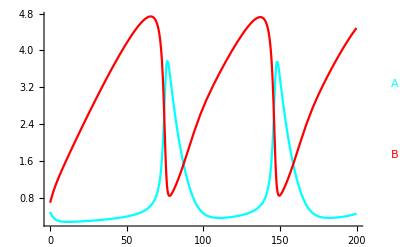

```mathematica
net={{∅⇄A,k1, k2},{2 A+B->3 A,k3},{A->B,k4}};
parameters={k1-> .1, k2-> .1, k3-> .1 ,k4-> .3, DA-> 0.1, DB-> 0.05};
s=run[net/.parameters, timeSpan-> 200, initialConditions-> {A-> .5, B-> .7}];
runPlot[s]
```

## Expand the network to all cells and run a simulation

```mathematica
ic[i_]:={A[i]->RandomReal[{0,5}],B[i]->RandomReal[{0,5}]};
myic=Flatten[ic/@Range[n]];
```

```mathematica
bignet=CelleratorNetwork[w, "Reactions"-> net, "Diffusion"-> {{A, DA}, {B,DB}}];
```

4 Cells.

4 internal reactions in each cell.

16 intracellular reactions.

16 diffusion reactions.

32 total reactions.

Run a simulation using xlr8r

```mathematica
sim=RunSim[bignet,parameters,myic,{0,1000}];
```

```mathematica
SolutionVariables[sim]
```

{A[1],A[2],A[3],A[4],B[1],B[2],B[3],B[4]}

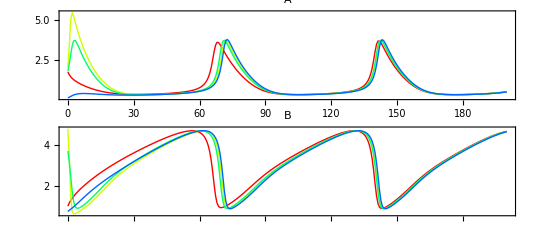

```mathematica
GraphicsColumn[SimPlot[sim,{A, B},{0,200}, AspectRatio->.2,ImageSize->500,"Points"->300]]
```